```mathematica
Clear["Global`*"]
pitchEXP=Import[NotebookDirectory[]<>"../SPHERIC_TestCase12/Rotation.dat"][[1;;]];
pitchEXP[[1]]
pitchEXP=pitchEXP[[2;;]];
motionsEXP=Import[NotebookDirectory[]<>"../SPHERIC_TestCase12/Motions.dat"][[1;;]];
motionsEXP[[1]]
heaveEXP={#1,#2}&@@@motionsEXP[[2;;,{1,2}]];
surgeEXP=motionsEXP[[2;;,{3,4}]];
```

{Time,(s),Roll,(degrees)}

{Time,(s),Heave,(m),Time,(s),Sway,(m)}

```mathematica
name="~/BEM/Hadzic2005/result.json";
imported=ImportString[StringReplace[Import[name,"text"],{"NaN"->"null","nan"->"null"}],"JSON"];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
titles=imported[[;;,1]];
Column[titles,Background->{{LightRed,Pink}},Frame->True]
```

cpu_time
float_COM
float_EK
float_EP
float_accel
float_area
float_force
float_pitch
float_roll
float_torque
float_velocity
float_yaw
simulation_time
wall_clock_time
water_E
water_EK
water_EP
water_volume

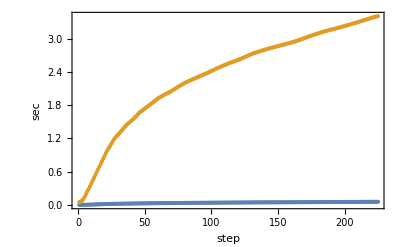

```mathematica
ListPlot[{getData["simulation_time"]/60,getData["simulation_time"]}
,Frame->True
,FrameLabel->{"step","sec"}
]
```

```mathematica
ListPlot[Transpose[{getData["simulation_time"],getData["float_force"]}]]
```

-Graphics-

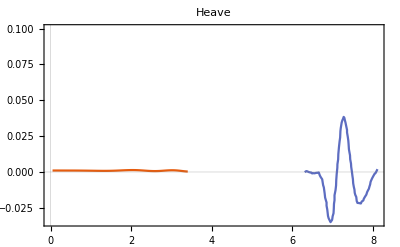

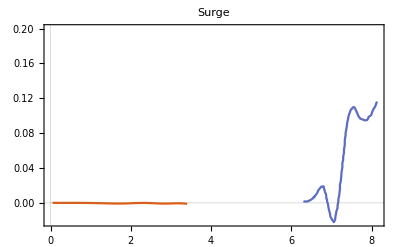

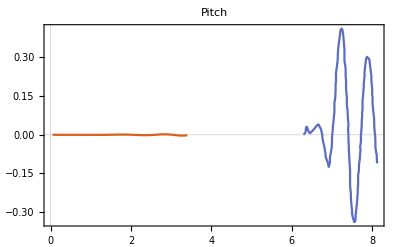

```mathematica
ListPlot[{Transpose[{getData["simulation_time"],getData["float_COM",3]-0.39}],{#1,#2}&@@@heaveEXP},PlotLabel->"Heave",PlotRange->{All,0.1},Joined->True,PlotTheme->"Scientific"]
ListPlot[{Transpose[{getData["simulation_time"],getData["float_COM",1]-2.11}],{#1,#2}&@@@surgeEXP},PlotLabel->"Surge",PlotRange->{All,0.2},PlotRange->All,Joined->True,PlotTheme->"Scientific"]
ListPlot[{Transpose[{getData["simulation_time"],getData["float_pitch"]}],{#1,-#2/180*Pi}&@@@pitchEXP},PlotLabel->"Pitch",PlotRange->All,Joined->True,PlotTheme->"Scientific"]
```

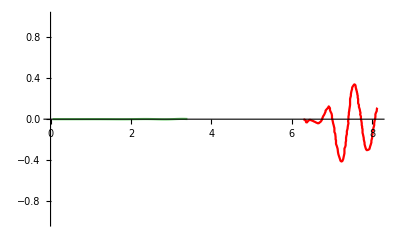

```mathematica
ListPlot[
{Transpose[{getData["simulation_time"],-getData["float_pitch"]}],
{#1,#2/180*Pi}&@@@pitchEXP},
PlotStyle->{{Darker[Green],Opacity[0.6]},{Red},{Dashed,Blue,Opacity[0.6]},{Thick}},
Joined->{True,True,True},
PlotRange->{Automatic,{-1,1}}
(*PlotRange->{{0,2.25},{-1.,1.}},*)
(*PlotTheme->"Scientific",
Frame->True,
Mesh->All,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,Italic],Style["H/H_0",FontSize->20,Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotTheme->"Scientific",
ImageSize->500,
PlotLegends->Placed[LineLegend[{"Measured Data","Simulated Data"},LegendMarkerSize->20,LabelStyle->20],{0.75,0.15}]*)
]
```